```mathematica
c=2.99792*^8;h=6.626*^-34;Hart=4.35974*^-18;
```

```mathematica
γgrd={0.543,4.148,0.08,0.67,0.01,0.21,2.04};
ωgrd={17992.007,25068.222,38174.17,40563.97,43659.38,44017.60,28857.014};Egrd={0,0,0,0,0,0,0};
For[i=1,i≤7,i++,
Egrd[[i]]=h*c*(ωgrd[[i]]*100)/Hart;
]
```

```mathematica
αsgrd[ω_]=2/(3*1)*Sum[γgrd[[i]]^2*Egrd[[i]]/(Egrd[[i]]^2-ω^2),{i,1,7}]+7.27;
```

```mathematica
γ3P1={0.58,2.57,4.45,0.46,1.57,2.72,0.53,2.47,1.67,0.86,3.47,0.24,1,.29,2.59,.18,2.92};
ω3P1={0,24489.102,24751.948,27677.665,39808.72,39838.04,40061.51,44311.38,44313.05,44357.60,32694.692,34350.65,41615.04,41939.90,42436.91,43805.42,44760.37};
J3P1={0,1,2,2,1,2,2,1,2,2,1,0,1,0,0,1,2};
E3P1={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
For[i=1,i≤17,i++,
E3P1[[i]]=h*c*(ω3P1[[i]]*100)/Hart;
]
```

```mathematica
1/((ω3P1-17992.007))/100
```

{-5.55802×10^-7,1.53915×10^-6,1.4793×10^-6,1.03245×10^-6,4.58364×10^-7,4.57749×10^-7,4.53114×10^-7,3.79948×10^-7,3.79924×10^-7,3.79282×10^-7,6.80148×10^-7,6.11298×10^-7,4.23316×10^-7,4.17573×10^-7,4.09083×10^-7,3.87395×10^-7,3.73575×10^-7}

```mathematica
αs3P1[ω_]=2/(3*3)*Sum[γ3P1[[i]]^2*(E3P1[[i]]-Egrd[[1]])/((E3P1[[i]]-Egrd[[1]])^2-ω^2),{i,1,17}]+7.27;
αt3P1[ω_,mF_]=4*(5*1*1/(6*2*3*5))^.5*Sum[(-1)^(1+J3P1[[i]])*(-1)^(1+1+1+1)*(*If[mF≤J3P1[[i]],1,0]*)SixJSymbol[{1,1,J3P1[[i]]},{1,1,2}]*γ3P1[[i]]^2*(E3P1[[i]]-Egrd[[1]])/((E3P1[[i]]-Egrd[[1]])^2-ω^2),{i,1,17}];
```

```mathematica
αtot3P1[ω_,F_,mF_,θ_]=αs3P1[ω]+(3*Cos[θ]^2-1)/2*If[F==1/2,0,(3*mF^2-F*(F+1))/(F*(2F-1))]*αt3P1[ω,mF];
```

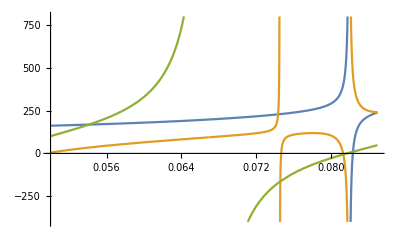

```mathematica
Plot[{αsgrd[ω],αtot3P1[ω,1,0,0],αtot3P1[ω,1,1,0]},{ω,.05,0.085},PlotRange-> {-400,800}]
```

```mathematica
1/18135./100
```

5.5142×10^-7

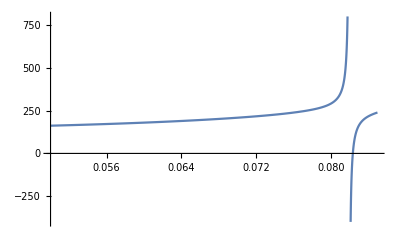

```mathematica
Plot[αsgrd[ω],{ω,0.05,0.085},PlotRange->{-400,800}]
```

```mathematica
(3*mF^2-F*(F+1))/(F*(2F-1))/.F->1/.mF->1
```

1

```mathematica
SixJSymbol[{1,1,2},{1,1,2}]
```

1/30

```mathematica
h*c/(759*^-9)/Hart
```

0.0600301

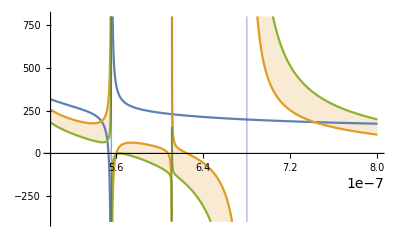

```mathematica
Fx=3/2;mFx=1/2;Plot[{αsgrd[c/(ω*Hart/h)],αtot3P1[c/(ω*Hart/h),Fx,mFx,0],αtot3P1[c/(ω*Hart/h),Fx,mFx,Pi/2]},{ω,500*^-9,800*^-9},Filling->{2-> {3}},PlotRange-> {-400,800}]
```

```mathematica
Jp={0,1,2,2,1,2,2,1,2,2,1,0,1,0, 0,1,2};
```

```mathematica
Lp={0,2,2,2,2,2,2,2,2,2,0,0,0,0,1,1,1};
```

```mathematica
ωp={{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
For[k=1,k≤17,k++,
ωp[[1,k]]=c*2Pi*(ω3P1[[k]]-17992.007)*100;
]
```

```mathematica
λp=c/(ωp/(2Pi));
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
For[i=1,i≤17,i++,
λp[[2,i]]=1/(1/λp[[1,i]]+(17288.439*100)-17992.007*100);
λp[[3,i]]=1/(1/λp[[1,i]]+(17288.439*100)-19710.388*100);
]
```

```mathematica
ωp=2*Pi*c/λp;
```

```mathematica
totbr[nt_]:=(Sqrt[(2*Jp[[nt]]+1)*(2*0+1)]*SixJSymbol[{Lp[[nt]],Jp[[nt]],1},{0,1,1}])^2*ωp[[0+1,nt]]^3+
(Sqrt[(2*Jp[[nt]]+1)*(2*1+1)]*SixJSymbol[{Lp[[nt]],Jp[[nt]],1},{1,1,1}])^2*ωp[[1+1,nt]]^3+
(Sqrt[(2*Jp[[nt]]+1)*(2*2+1)]*SixJSymbol[{Lp[[nt]],Jp[[nt]],1},{2,1,1}])^2*ωp[[2+1,nt]]^3;
```

```mathematica
br[jbr_,nbr_]:=(Sqrt[(2*Jp[[nbr]]+1)*(2*jbr+1)]*SixJSymbol[{Lp[[nbr]],Jp[[nbr]],1},{jbr,1,1}])^2*ωp[[jbr+1,nbr]]^3/totbr[nbr];
```

```mathematica
Sqrt[(2*Jp[[nbr]]+1)*(2*jbr+1)]*SixJSymbol[{Lp[[nbr]],Jp[[nbr]],1},{jbr,1,1}]/.jbr->0/.nbr->15
```

Part::pkspec1: The expression nbr cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

0

```mathematica
For[i=2,i≤17,i++,
Print[br[0,i],"\t",br[1,i],"\t",br[2,i]];
]
```

0.647619	0.344391	0.00799026

0.	0.890875	0.109125

0.	0.850132	0.149868

0.58313	0.396385	0.0204843

0.	0.794607	0.205393

0.	0.794154	0.205846

0.578411	0.39994	0.0216488

0.	0.786996	0.213004

0.	0.786934	0.213066

0.153767	0.398195	0.448039

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Indeterminate	Indeterminate	Indeterminate

0.135976	0.372553	0.491471

Indeterminate	Indeterminate	Indeterminate

0.	1.	0.

0.381612	0.263438	0.35495

0.	0.290283	0.709717

```mathematica
totbr[15]
```

2.98122×10^46

```mathematica
Δ={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
```

```mathematica
Δ=Abs[ωp]-(2Pi*c/(532*^-9));
```

```mathematica
Γ=γ3P1^2;
```

```mathematica
For[i=1,i≤17,i++,
Print[Γ[[i]]/(Δ[[1,i]])^2*1*^32];
]
```

1463.12

123.045

385.194

7.18376

761.844

2242.91

73.9247

303.867

138.845

36.3886

2024.41

27.3043

121.009

8.93367

592.685

1.85487

378.181